Getting the data...

Done.

μ_η

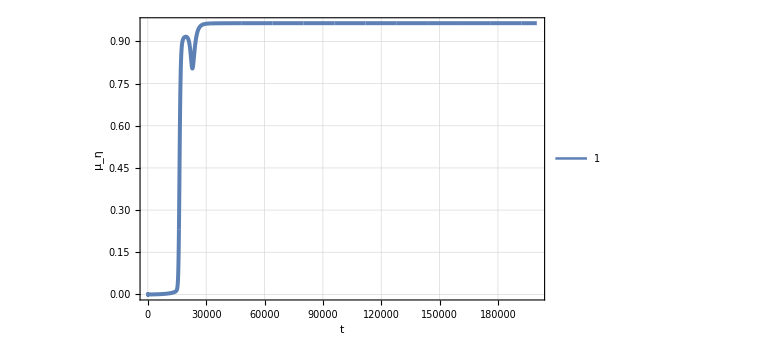

=========================================

μ_η

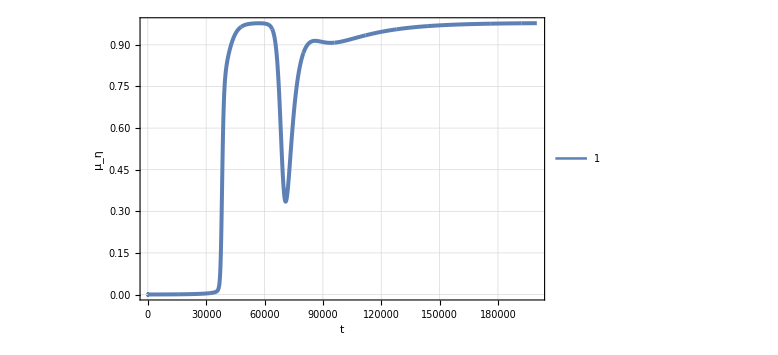

=========================================

μ_η

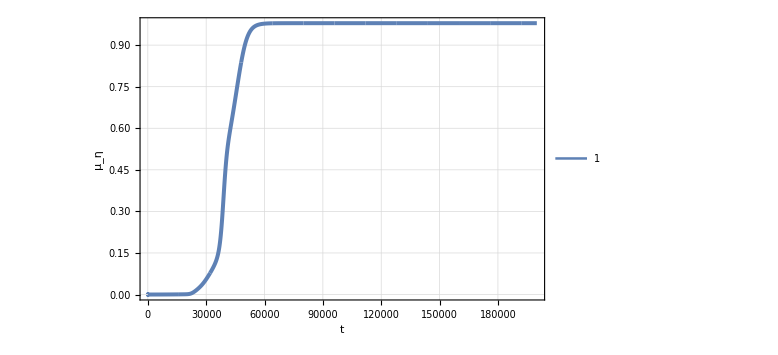

=========================================

μ_η

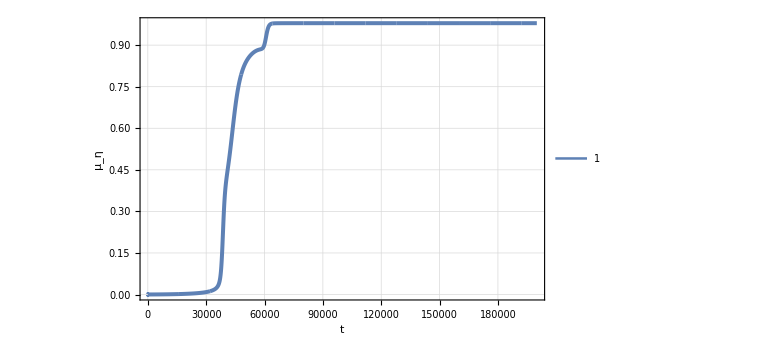

=========================================

μ_η

-Graphics-

=========================================

=========================================

=========================================

μ_η

-Graphics-

=========================================

σ_η

-Graphics-

=========================================

μ_ζ

-Graphics-

=========================================

σ_ζ

-Graphics-

=========================================

u_total

-Graphics-

=========================================

food

-Graphics-

=========================================

waste

-Graphics-

=========================================

```mathematica
Print["Getting the data..."];
Get["C:\\GitHub\\CoreClm\\Math\\odePackChartSupport.m"];
Get["C:\\GitHub\\FindUniversity\\ClmFsharp\\ISSOL2023\\EeInf\\allData__200K.m"];
Print["Done."];

dataSource = allData;
divisor = 1;
(* {d500k1e01g01a005i10f1E$200K,d500k1e005g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e005g01a005f1E$200K,d500k1e005g01a005i10f1E$200K} *)

plotCombinedChart[{d500k1e01g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];
plotCombinedChart[{d500k1e005g01a002f1E$200K},2,Subscript["μ","η"],divisor];
plotCombinedChart[{d500k1e005g01a002i10f1E$200K},2,Subscript["μ","η"],divisor];
plotCombinedChart[{d500k1e005g01a005f1E$200K},2,Subscript["μ","η"],divisor];
plotCombinedChart[{d500k1e005g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];

(* ================================================== *)
Print[sep];
Print[sep];

plotCombinedChart[dataSource,2,Subscript["μ","η"],divisor];
plotCombinedChart[dataSource,3,Subscript["σ","η"],divisor];
plotCombinedChart[dataSource,4,Subscript["μ","ζ"],divisor];
plotCombinedChart[dataSource,5,Subscript["σ","ζ"],divisor];
plotCombinedChart[dataSource,7,Subscript["u","total"],divisor];
plotCombinedChart[dataSource,8,"food",divisor];
plotCombinedChart[dataSource,9,"waste",divisor];
```